```mathematica
y=1/π(π/2+ArcTan[α x]);
f=FullSimplify[Log[y/(1-y)]]
```

{-10.9969,-10.9428,-10.8857,-10.8251,-10.7605,-10.6915,-10.6174,-10.5374,-10.4504,-10.355,-10.2497,-10.1319,-9.99835,-9.84419,-9.66186,-9.4387,-9.15099,-8.74547,-8.05217,0.,8.05217,8.74547,9.15099,9.4387,9.66186,9.84419,9.99835,10.1319,10.2497,10.355,10.4504,10.5374,10.6174,10.6915,10.7605,10.8251,10.8857,10.9428,10.9969}

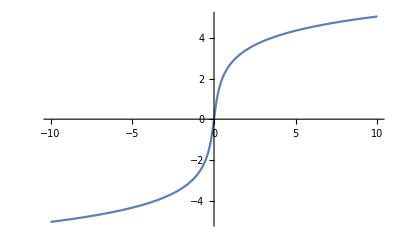

```mathematica
Clear[x,y];
y=Log[(π+2 ArcTan[x α])/(π-2 ArcTan[x α])];
Table[y/.{α->5},{x,-3800.0, 3800.0, 200}]
Plot[y/.α->5,{x,-10,10}]
```

3811.77

(ⅇ^y π Csc[π/(1+ⅇ^y)]^2)/((1+ⅇ^y)^2 α)

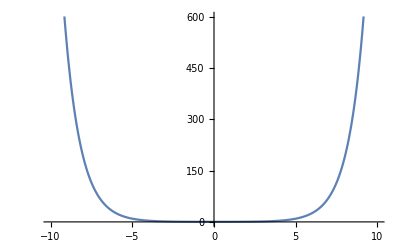

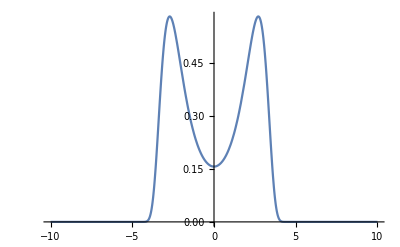

```mathematica
Clear[x,y];
x=1/α Tan[π/2(ⅇ^y-1)/(ⅇ^y+1)];
x/.{y->11.0,α->5}
J=FullSimplify[D[x,y]]
Plot[J/.α->5,{y,-10,10}]
Plot[Exp[-1/2 x^2]J/.α->5,{y,-10,10}]
```